```mathematica
(* ============================================================*)(*Direct Fourier-Domain Monte Carlo Variance Verification*)(*With parallelization and corrected sign conventions*)(* ============================================================*)(*Clear any existing definitions*)ClearAll["Global`*"];

(*---Initialize Parallel Kernels---*)
If[Length[Kernels[]]==0,LaunchKernels[];];
Print["Using ",Length[Kernels[]]," parallel kernels."];

(*---Core Functions---*)

transferMagnitude[γ2_]:=Sqrt[γ2]

singleSegmentQuantities[{A_,B_,H_,J_},γ2_,ϕ_,P_:1]:=Module[{Tmag,Tr,Ti,K,Xr,Xi,Yr,Yi,Cr,Ci,PXseg,PYseg},Tmag=transferMagnitude[γ2];
Tr=Tmag Cos[ϕ];
Ti=Tmag Sin[ϕ];
K=Sqrt[P (1-γ2)/2];
Xr=Sqrt[P/2] A;
Xi=Sqrt[P/2] B;
Yr=K H+(Tr Xr-Ti Xi);
Yi=K J+(Tr Xi+Ti Xr);
Cr=Xr Yr+Xi Yi;
Ci=Xi Yr-Xr Yi;
PXseg=Xr^2+Xi^2;
PYseg=Yr^2+Yi^2;
{Cr,Ci,PXseg,PYseg}]

estimateCoherencePhase[{Crbar_,Cibar_,PXbar_,PYbar_}]:=Module[{γ2hat,ϕhat},γ2hat=(Crbar^2+Cibar^2)/(PXbar PYbar);
ϕhat=ArcTan[Crbar,Cibar];
{γ2hat,ϕhat}]

(*Single trial-fully sequential,will be called from parallel context*)
singleTrial[n_,γ2target_,ϕtarget_,P_:1]:=Module[{randomVectors,segmentQuantities,averaged},randomVectors=RandomVariate[NormalDistribution[0,1],{n,4}];
segmentQuantities=singleSegmentQuantities[#,γ2target,ϕtarget,P]&/@randomVectors;
averaged=Mean[segmentQuantities];
estimateCoherencePhase[averaged]]

(*Monte Carlo with parallel trials*)
monteCarloVariance[M_,n_,γ2target_,ϕtarget_,P_:1]:=Module[{trials,γ2estimates,ϕestimates},(*Parallelize over M trials*)trials=ParallelTable[singleTrial[n,γ2target,ϕtarget,P],{M},Method->"CoarsestGrained"];
γ2estimates=trials[[All,1]];
ϕestimates=trials[[All,2]];
{Variance[γ2estimates],Variance[ϕestimates]}]

(*Analytic predictions*)
analyticVarianceγ2[γ2_,n_]:=2 γ2 (1-γ2)^2/n
analyticVarianceϕ[γ2_,n_]:=(1-γ2)/(2 n γ2)

(*Distribute definitions to kernels*)
DistributeDefinitions[transferMagnitude,singleSegmentQuantities,estimateCoherencePhase,singleTrial];

(* ============================================================*)
(*Run the Simulation*)
(* ============================================================*)

M=1000;
nValues={10,20,50,100,200,500,1000,2000,5000};
γ2Values={0.1,0.333,0.5,0.7,0.9};
ϕTarget=0;

Print["Running Monte Carlo simulation..."];
Print["Testing ",Length[γ2Values]," coherence values × ",Length[nValues]," segment counts"];
Print["Start time: ",DateString[]];

timing=AbsoluteTiming[results=Table[Print["  Processing γ.b2 = ",γ2,", n = ",n];
{γ2,n,monteCarloVariance[M,n,γ2,ϕTarget]},{γ2,γ2Values},{n,nValues}]//Flatten[#,1]&;][[1]];

Print["Done. Elapsed time: ",Round[timing,0.1]," seconds"];

(*Restructure results*)
resultsTable={#[[1]],#[[2]],#[[3,1]],#[[3,2]]}&/@results;

(* ============================================================*)
(*Plotting*)
(* ============================================================*)
```

Using 11 parallel kernels.

Running Monte Carlo simulation...

Testing 5 coherence values × 9 segment counts

Start time: Fri 23 Jan 2026 12:08:37

Processing γ.b2 = 0.1, n = 10

Processing γ.b2 = 0.1, n = 20

Processing γ.b2 = 0.1, n = 50

Processing γ.b2 = 0.1, n = 100

Processing γ.b2 = 0.1, n = 200

Processing γ.b2 = 0.1, n = 500

Processing γ.b2 = 0.1, n = 1000

Processing γ.b2 = 0.1, n = 2000

Processing γ.b2 = 0.1, n = 5000

Processing γ.b2 = 0.333, n = 10

Processing γ.b2 = 0.333, n = 20

Processing γ.b2 = 0.333, n = 50

Processing γ.b2 = 0.333, n = 100

Processing γ.b2 = 0.333, n = 200

Processing γ.b2 = 0.333, n = 500

Processing γ.b2 = 0.333, n = 1000

Processing γ.b2 = 0.333, n = 2000

Processing γ.b2 = 0.333, n = 5000

Processing γ.b2 = 0.5, n = 10

Processing γ.b2 = 0.5, n = 20

Processing γ.b2 = 0.5, n = 50

Processing γ.b2 = 0.5, n = 100

Processing γ.b2 = 0.5, n = 200

Processing γ.b2 = 0.5, n = 500

Processing γ.b2 = 0.5, n = 1000

Processing γ.b2 = 0.5, n = 2000

Processing γ.b2 = 0.5, n = 5000

Processing γ.b2 = 0.7, n = 10

Processing γ.b2 = 0.7, n = 20

Processing γ.b2 = 0.7, n = 50

Processing γ.b2 = 0.7, n = 100

Processing γ.b2 = 0.7, n = 200

Processing γ.b2 = 0.7, n = 500

Processing γ.b2 = 0.7, n = 1000

Processing γ.b2 = 0.7, n = 2000

Processing γ.b2 = 0.7, n = 5000

Processing γ.b2 = 0.9, n = 10

Processing γ.b2 = 0.9, n = 20

Processing γ.b2 = 0.9, n = 50

Processing γ.b2 = 0.9, n = 100

Processing γ.b2 = 0.9, n = 200

Processing γ.b2 = 0.9, n = 500

Processing γ.b2 = 0.9, n = 1000

Processing γ.b2 = 0.9, n = 2000

Processing γ.b2 = 0.9, n = 5000

Done. Elapsed time: 181.5 seconds

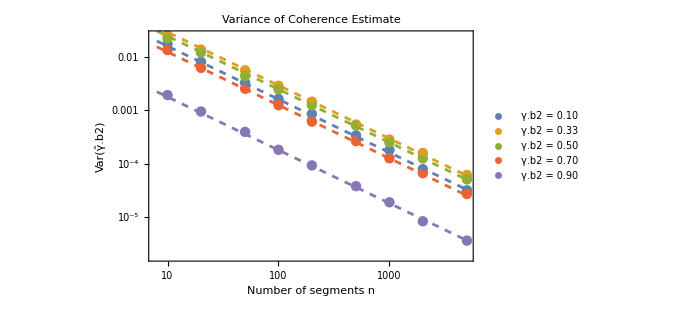

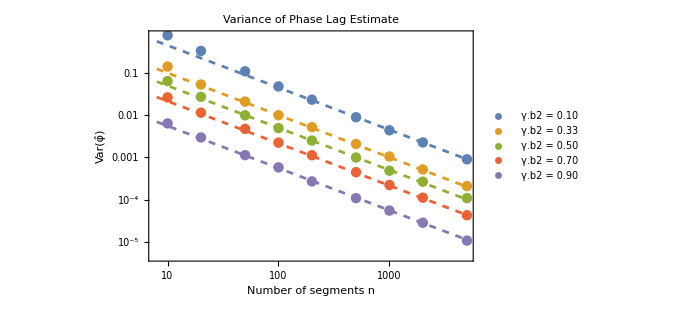

```mathematica
dataForPlotγ2=Table[Select[resultsTable,#[[1]]==γ2&][[All,{2,3}]],{γ2,γ2Values}];

dataForPlotϕ=Table[Select[resultsTable,#[[1]]==γ2&][[All,{2,4}]],{γ2,γ2Values}];

colors=ColorData[97]/@Range[Length[γ2Values]];

plotγ2=Show[ListLogLogPlot[dataForPlotγ2,PlotStyle->(Directive[#,PointSize[0.015]]&/@colors),PlotLegends->Placed[LineLegend[colors,(Row[{"γ.b2 = ",NumberForm[#,{3,2}]}]&/@γ2Values)],{0.75,0.7}],PlotRange->All],LogLogPlot[Evaluate[analyticVarianceγ2[#,n]&/@γ2Values],{n,8,Max[nValues]},PlotStyle->(Directive[#,Dashed]&/@colors),PlotRange->All],Frame->True,FrameLabel->{"Number of segments n","Var(γ̂.b2)"},PlotLabel->"Variance of Coherence Estimate",ImageSize->500]

plotϕ=Show[ListLogLogPlot[dataForPlotϕ,PlotStyle->(Directive[#,PointSize[0.015]]&/@colors),PlotLegends->Placed[LineLegend[colors,(Row[{"γ.b2 = ",NumberForm[#,{3,2}]}]&/@γ2Values)],{0.75,0.7}],PlotRange->All],LogLogPlot[Evaluate[analyticVarianceϕ[#,n]&/@γ2Values],{n,8,Max[nValues]},PlotStyle->(Directive[#,Dashed]&/@colors),PlotRange->All],Frame->True,FrameLabel->{"Number of segments n","Var(φ̂)"},PlotLabel->"Variance of Phase Lag Estimate",ImageSize->500]

(*combinedPlot=GraphicsRow[{plotγ2,plotϕ},ImageSize->1000,Spacings->0]*)
```

```mathematica
(* ============================================================*)
(*Numerical Verification*)
(* ============================================================*)

Print["\n=== Numerical Verification ===\n"];

Table[Module[{data,scaledVars,analyticPrefactor,meanScaled},data=Select[resultsTable,#[[1]]==γ2&];
scaledVars=#[[3]]*#[[2]]&/@data;
analyticPrefactor=2 γ2 (1-γ2)^2;
meanScaled=Mean[scaledVars];
Print["γ.b2 = ",NumberForm[γ2,{3,3}],"  |  Analytic: ",NumberForm[analyticPrefactor,{4,4}],"  |  MC mean(Var×n): ",NumberForm[meanScaled,{4,4}],"  |  Ratio: ",NumberForm[meanScaled/analyticPrefactor,{3,2}]];],{γ2,γ2Values}];

Print["\n--- Phase lag variance ---\n"];

Table[Module[{data,scaledVars,analyticPrefactor,meanScaled},data=Select[resultsTable,#[[1]]==γ2&];
scaledVars=#[[4]]*#[[2]]&/@data;
analyticPrefactor=(1-γ2)/(2 γ2);
meanScaled=Mean[scaledVars];
Print["γ.b2 = ",NumberForm[γ2,{3,3}],"  |  Analytic: ",NumberForm[analyticPrefactor,{4,4}],"  |  MC mean(Var×n): ",NumberForm[meanScaled,{4,4}],"  |  Ratio: ",NumberForm[meanScaled/analyticPrefactor,{3,2}]];],{γ2,γ2Values}];

(* ============================================================*)
(*Optional:Test φ-independence*)
(* ============================================================*)

Print["\n=== Testing φ-independence ===\n"];

ϕTestValues={0,π/4,π/2,3π/4,π};
γ2Test=0.5;
nTest=100;

ϕIndependenceResults=Table[{ϕ,monteCarloVariance[M,nTest,γ2Test,ϕ]},{ϕ,ϕTestValues}];

Print["For γ.b2 = ",γ2Test,", n = ",nTest,":"];
Print["Analytic Var(γ̂.b2) = ",analyticVarianceγ2[γ2Test,nTest]];
Print["Analytic Var(φ̂) = ",analyticVarianceϕ[γ2Test,nTest]];
Print[""];
Print[TableForm[{NumberForm[#[[1]]/π,{2,2}],#[[2,1]],#[[2,2]]}&/@ϕIndependenceResults,TableHeadings->{None,{"φ/π","Var(γ̂.b2)","Var(φ̂)"}}]];
```

=== Numerical Verification ===

γ.b2 = 0.100  |  Analytic: 0.1620  |  MC mean(Var×n): 0.1678  |  Ratio: 1.04

γ.b2 = 0.333  |  Analytic: 0.2963  |  MC mean(Var×n): 0.2875  |  Ratio: 0.97

γ.b2 = 0.500  |  Analytic: 0.2500  |  MC mean(Var×n): 0.2463  |  Ratio: 0.99

γ.b2 = 0.700  |  Analytic: 0.1260  |  MC mean(Var×n): 0.1296  |  Ratio: 1.03

γ.b2 = 0.900  |  Analytic: 0.0180  |  MC mean(Var×n): 0.0186  |  Ratio: 1.03

--- Phase lag variance ---

γ.b2 = 0.100  |  Analytic: 4.5000  |  MC mean(Var×n): 5.2430  |  Ratio: 1.17

γ.b2 = 0.333  |  Analytic: 1.0020  |  MC mean(Var×n): 1.0800  |  Ratio: 1.08

γ.b2 = 0.500  |  Analytic: 0.5000  |  MC mean(Var×n): 0.5248  |  Ratio: 1.05

γ.b2 = 0.700  |  Analytic: 0.2143  |  MC mean(Var×n): 0.2280  |  Ratio: 1.06

γ.b2 = 0.900  |  Analytic: 0.0556  |  MC mean(Var×n): 0.0566  |  Ratio: 1.02

=== Testing φ-independence ===

For γ.b2 = 0.5, n = 100:

Analytic Var(γ̂.b2) = 0.0025

Analytic Var(φ̂) = 0.005

φ/π | Var(γ̂.b2) | Var(φ̂)
0 | 0.00252681 | 0.00506076
1/4 | 0.0025589 | 0.00488333
1/2 | 0.00253266 | 0.00477116
3/4 | 0.00241321 | 0.00513194
1 | 0.00238166 | 9.49928